# Use all 1/3 vertices

## Depict Tiles

```mathematica
TileVertices[step_][or_,dir_,ref_,pt_] := With[{
basicVertices = AnglePath[{
		{step[[2]], -Pi/6+dir*Pi/6},
		{step[[2]], Pi/3},
		{step[[1]], Pi/2},
		{step[[1]], Pi/3},
		{step[[2]], -Pi/2},
		{step[[2]], Pi/3},
		{step[[1]], Pi/2},
		{step[[1]], -Pi/3},
		{step[[2]], Pi/2},
		{step[[2]], -Pi/3},
		{step[[1]], Pi/2},
		{step[[1]], Pi/3},
		{step[[1]], 0}
	}]
},
	Expand[# + or&/@(If[ref,{-#[[1]],#[[2]]},#]&/@((#-basicVertices[[pt]])&/@basicVertices))]
]
```

```mathematica
TileEdges[step_][or_,dir_,ref_,pt_] := Partition[TileVertices[step][or,dir,ref,pt], 2, 1, 1]
```

```mathematica
Tile[step_][or_,dir_,ref_,pt_] := Polygon[TileVertices[step][or,dir,ref,pt]]
```

```mathematica
hatVertices:=TileVertices[{1, Sqrt[3]}];
hatEdges:=TileEdges[{1, Sqrt[3]}];
hat:=Tile[{1, Sqrt[3]}];
```

```mathematica
spectreVertices:=TileVertices[{1,1}];
spectreEdges:=TileEdges[{1,1}];
spectre:=Tile[{1,1}];
```

```mathematica
canonicalHat[or_,dir_,ref_,pt_]:={hatVertices[or,dir,ref,pt][[1]], dir, ref, 1}
```

## Manipulate Cluster

```mathematica
rotateCluster[code_,r_]:=Replace[code,
{
{pos_,dir_,False,pt_}:>{Expand[RotationMatrix[r*Pi/6].pos],Mod[dir+r,12],False,pt},
{pos_,dir_,True,pt_}:>{Expand[RotationMatrix[r*Pi/6].pos],Mod[dir-r,12],True,pt}
},
{1}
];

translateCluster[code_,vec_]:={#1+vec,#2,#3,#4}&@@@code;

placeCluster[pos_,dir_,code_]:=translateCluster[rotateCluster[code,dir],pos];
```

```mathematica
rotateTiling[tiling_, r_] := <|
	"code" -> rotateCluster[tiling["code"], r],
	"controlPoints" -> (Expand[RotationMatrix[r * Pi/6] . #] & /@ tiling["controlPoints"])
|>

translateTiling[tiling_, vec_] := <|
	"code" -> translateCluster[tiling["code"], vec],
	"controlPoints" -> (Expand[# + vec] & /@ tiling["controlPoints"])
|>

placeTiling[pos_, dir_, tiling_] := translateTiling[rotateTiling[tiling, dir], pos];
```

```mathematica
reflectCode[code_]:=Apply[{{-#1,#2}&@@#1,#2,#3/.{True->False,False->True},#4}&,code,{1}];
reflectTiling[tiling_] := <|"code"->reflectCode[tiling["code"]],"controlPoints"->Apply[{-#1,#2}&,tiling["controlPoints"],1]|>
```

## Substitution Rule

```mathematica
substitute[t1_,t2_]:=With[
{
tiling1=translateTiling[t1,-t1["controlPoints"][[1]]],
tiling2=translateTiling[t2,-t2["controlPoints"][[1]]]
},
Block[{T1,T2,T3,T4,T5,T6,T7,T8},
T1=tiling2;
T2=tilingPlace[tiling2][T1["controlPoints"][[1]],4,1];
T3=tilingPlace[tiling2][T2["controlPoints"][[2]],2,5];
T4=tilingPlace[tiling1][T3["controlPoints"][[2]],0,5];
T5=tilingPlace[tiling2][T4["controlPoints"][[4]],0,1];
T6=tilingPlace[tiling2][T5["controlPoints"][[2]],10,5];
T7=tilingPlace[tiling2][T6["controlPoints"][[2]],8,5];
T8=tilingPlace[tiling2][T1["controlPoints"][[1]],0,4];
Sow[{T1,T2,T3,T4,T5,T6,T7,T8}];
<|"tiling1"-><|
"code"->Join@@(#["code"]&/@{T2,T3,T4,T5,T6,T7}),
"controlPoints"->{
T2["controlPoints"][[5]],
T7["controlPoints"][[4]],
T6["controlPoints"][[4]],
T5["controlPoints"][[5]],
T3["controlPoints"][[4]]
}
|>,
"tiling2"-><|
"code"->Join@@(#["code"]&/@{T1,T2,T3,T4,T5,T6,T7}),
"controlPoints"->{
T2["controlPoints"][[5]],
T7["controlPoints"][[4]],
T6["controlPoints"][[4]],
T5["controlPoints"][[5]],
T3["controlPoints"][[4]]
}
|>
|>
]
];
```

## Visualization

```mathematica
Options[depictControlPoints]=Join[
Options[Graphics],
{
step->{1,Sqrt[3]},
ChooseColor->{LightBlue,Yellow},
EdgeForm->Black,
ShowControlPoints->True
}
];
depictControlPoints[tile_,opt:OptionsPattern[]]:=Graphics[
{
	tile["code"]/.{
			{pos_,or_,False,v_}:>
				{
Opacity[.6],EdgeForm[OptionValue[EdgeForm]],OptionValue[ChooseColor][[1]],
Tile[OptionValue[step]][pos,or,False,v]
},
			{pos_,or_,True,v_}:>
				{
Opacity[.6],EdgeForm[OptionValue[EdgeForm]],OptionValue[ChooseColor][[2]],
Tile[OptionValue[step]][pos,or,True,v]
}
	}
	,
If[
OptionValue[ShowControlPoints],
{
Red,PointSize[.03],
Point[tile["controlPoints"]],
Line[Partition[tile["controlPoints"],2,1,1]]
},
Nothing
]
}
,
Sequence@@FilterRules[{opt},Options[Graphics]]
];
```

## Tiles Information

### alternative H7 H8 H2 H1

```mathematica
AH7Tiling=<|
"code"->
,
"controlPoints"->((hatVertices@@@)[[##]]&@@@(
{{1,4},{3,2},{6,2},{7,4},{4,2}}
))
|>;
H8Tiling=<|
"code"->
,
"controlPoints"->((hatVertices@@@)[[##]]&@@@(
{{2,4},{4,2},{7,2},{8,4},{5,2}}
))
|>;
```

```mathematica
AH2Tiling=<|
"code"->{{{-3/2,-1/2 (3 √3)},2,True,11},{{-3,-√3},8,False,7}},
"controlPoints"->hatVertices[{-3,-√3},8,False,7][[{6,12,14,2,4}]]
|>;

H1Tiling=<|
"code"->{{{0,0},8,False,7}},
"controlPoints"->hatVertices[{0,0},8,False,7][[{6,12,14,2,4}]]
|>;
```

## Let fractal!!!

```mathematica
tilingPlace[tiling_][pos_,dir_,pt_]:=placeTiling[pos,dir,translateTiling[tiling,-tiling["controlPoints"][[pt]]]];
```

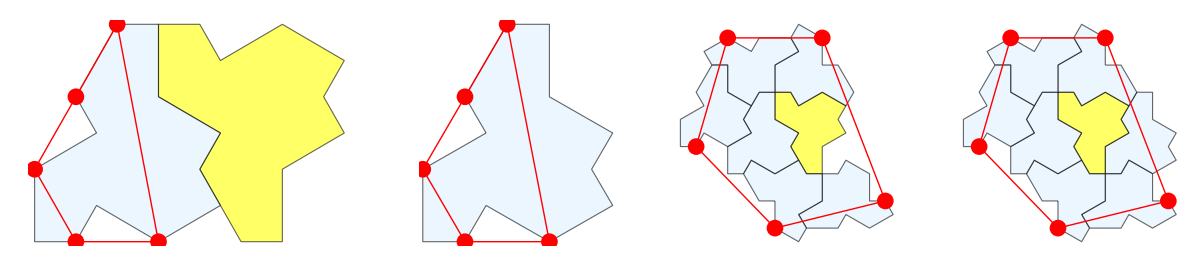

```mathematica
depictControlPoints/@{AH2Tiling,H1Tiling,AH7Tiling,H8Tiling}//GraphicsRow
```

```mathematica
supertiles=Reap[NestList[Values[substitute[#[[1]],#[[2]]]]&,{AH2Tiling,H1Tiling},5]];
```

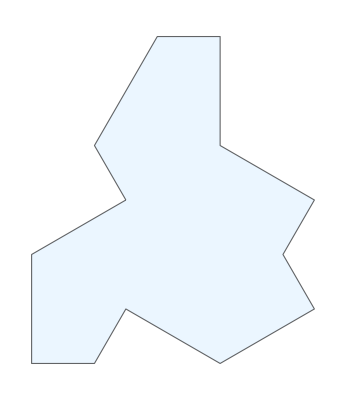
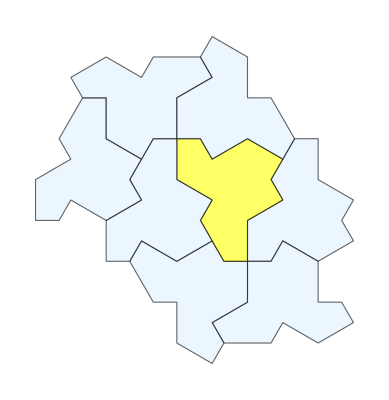
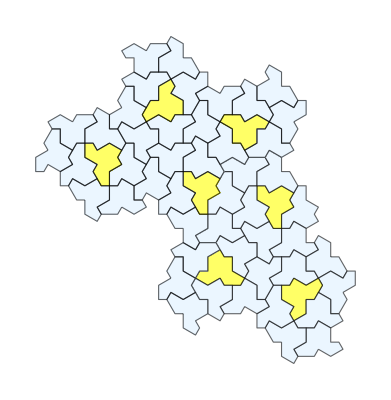
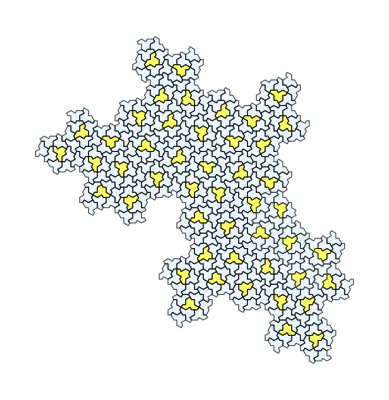
-Graphics-
↓
-Graphics-
↓
-Graphics-
↓
-Graphics-

```mathematica
(Map[Show[#,ImageSize->(-10Subtract@@@PlotRange/.AbsoluteOptions[#])]&@depictControlPoints[#,ShowControlPoints->False]&,supertiles[[1,;;4,2]]]//Riffle[#,Style["↓",Red,30]]&)//Column[#,Alignment->Center]&
```

```mathematica
Export[NotebookDirectory[]<>"Substitution(4-level).png",
(Map[Show[#,ImageSize->(-10Subtract@@@PlotRange/.AbsoluteOptions[#])]&@depictControlPoints[#,ShowControlPoints->False]&,supertiles[[1,;;4,2]]]//Riffle[#,Style["↓",Red,30]]&)//Column[#,Alignment->Center]&
]
```

C:\Users\hp\Desktop\Wolfram Summer School\project\Tile\FractalSubstitution\Substitution(4-level).png

## Export Video

```mathematica
substitutionProcess=Function[n,Show[#,ImageSize->1000]&@Show[Graphics[
{#["code"]/.{
			{pos_,or_,False,v_}:>
				{Opacity[1],EdgeForm[Directive[Black,Thick]],LightBlue,Tile[{1,Sqrt[3]}][pos,or,False,v]},
			{pos_,or_,True,v_}:>
				{Opacity[0.8],EdgeForm[Directive[Black,Thick]],Lighter@Blue,Tile[{1,Sqrt[3]}][pos,or,True,v]}}
(*,{Red,PointSize[0.03],Point[#["controlPoints"]],Line[Partition[#["controlPoints"],2,1,1]]}*)
}
]&/@#[[;;n]]]]/@Range[1,7]&/@{,,,};
```

```mathematica
Export[NotebookDirectory[]<>"\\Result\\subtitutingProcess"<>ToString[#]<>".mp4",
AnimationVideo[substitutionProcess[[#,i]],{i,1,7,1},DefaultDuration->7,CompressionLevel->0]
]&/@Range[Length[substitutionProcess]]
```

{C:\Users\hp\Desktop\Wolfram Summer School\project\Tile\FractalSubstitutionRule\\Result\subtitutingProcess1.mp4,C:\Users\hp\Desktop\Wolfram Summer School\project\Tile\FractalSubstitutionRule\\Result\subtitutingProcess2.mp4,C:\Users\hp\Desktop\Wolfram Summer School\project\Tile\FractalSubstitutionRule\\Result\subtitutingProcess3.mp4,C:\Users\hp\Desktop\Wolfram Summer School\project\Tile\FractalSubstitutionRule\\Result\subtitutingProcess4.mp4}

```mathematica
Export[NotebookDirectory[]<>"\\Result\\subtitutingProcess(0-3).mp4",
AnimationVideo[(Join@@substitutionProcess)[[i]],{i,1,28,1},CompressionLevel->0,DefaultDuration->14]
]
```

C:\Users\hp\Desktop\Wolfram Summer School\project\Tile\FractalSubstitutionRule\\Result\subtitutingProcess(0-3).mp4

## Dynamic Module

```mathematica
Manipulate[
Show[Graphics[
{#["code"]/.{
			{pos_,or_,False,v_}:>
				{Opacity[1],EdgeForm[Black],LightBlue,Tile[{1,Sqrt[3]}][pos,or,False,v]},
			{pos_,or_,True,v_}:>
				{Opacity[0.8],EdgeForm[Black],Lighter@Blue,Tile[{1,Sqrt[3]}][pos,or,True,v]}},
If[
TrueQ@ShowPoints,
{Red,PointSize[0.03],Point[#["controlPoints"]],Line[Partition[#["controlPoints"],2,1,1]]},
Nothing
]}
]&/@level[[;;i]]],
{i,1,7,1},
{
level,{->"Hat Tile",->"0-Supertile",->"1-Supertile"}
},
{
ShowPoints,{True,False}
},
SaveDefinitions->True
]
```

## 1/3 Vertex Theorem

1/3 Vertex Theorem represented by control points number:

```mathematica
oneThirdCombinatorics=;
```

For Hat tile

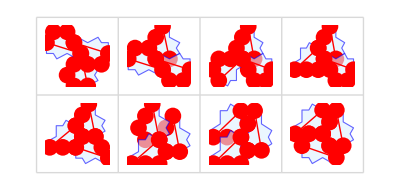

```mathematica
Map[
Show[depictControlPoints[#,ChooseColor->{LightBlue},ShowControlPoints->True]&/@#]&,
Apply[tilingPlace[H1Tiling][{0,0},##]&,oneThirdCombinatorics,{2}],
{1}
]//Partition[#,4]&//GraphicsGrid[#,Frame->All,FrameStyle->LightGray]&
```

For H8

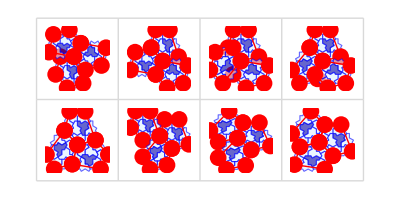

```mathematica
Map[
Show[depictControlPoints[#,ChooseColor->{LightBlue,Darker@Blue},ShowControlPoints->True]&/@#]&,
Apply[tilingPlace[H8Tiling][{0,0},##]&,oneThirdCombinatorics,{2}],
{1}
]//Partition[#,4]&//GraphicsGrid[#,Frame->All,FrameStyle->LightGray]&
```

For H8 1-super-tile

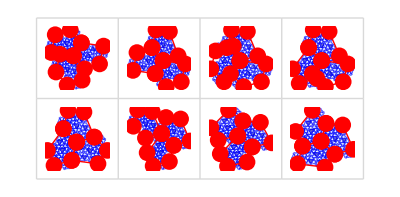

```mathematica
Map[
Show[depictControlPoints[#,ChooseColor->{LightBlue,Darker@Blue},ShowControlPoints->True]&/@#]&,
Apply[tilingPlace[supertiles[[1,3,2]]][{0,0},##]&,oneThirdCombinatorics,{2}],
{1}
]//Partition[#,4]&//GraphicsGrid[#,Frame->All,FrameStyle->LightGray]&
```